```mathematica
Fs[v_,g_,r_]:=Sqrt[1+(r-1)/Cos[g]^2*(1+r*(1-v^2))]
tanBp[v_,g_]:=2*v^2*Sin[g]*Cos[g]/(2*v^2*Sin[g]^2-1)
tanBs[v_,g_,r_]:=-tanBp[v,g]*Fs[v,g,r]
tanDs[v_,g_,r_]:=(tanBs[v,g,r]-tanBp[v,g])/(1+tanBs[v,g,r]*tanBp[v,g])
tanDpover2[v_,g_]:=-tanBp[v,g]
tanDp[v_,g_]:=2*tanDpover2[v,g]/(1-tanDpover2[v,g]^2)
tanDsover2[v_,g_,r_]:=(-1-Sqrt[1+tanDs[v,g,r]^2])/tanDs[v,g,r]
diff[v_,g_,r_]:=Abs[1-ArcTan[ 1,tanDs[v,g,r]]/ArcTan[1,tanDp[v,g]]]
diff2[v_,g_,r_]:=Abs[tanDp[v,g]-tanDs[v,g,r]]
diffTest[v_,g_,r_,p_]:=Piecewise[{{1,diff[v,g,r]>1},{diff[v,g,r],diff[v,g,r]≤1}}]
diffTest2[v_,g_,r_,p_]:=Piecewise[{{1,diff2[v,g,r]>p/100*Abs[tanDp[v,g]]},{0,diff2[v,g,r]<=p/100*Abs[tanDp[v,g]]}}]
```

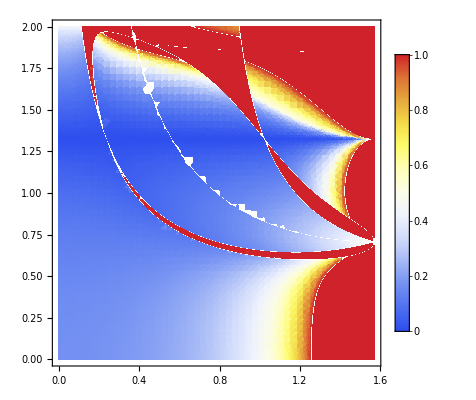

```mathematica
DensityPlot[diffTest[v,g,1.33,1],{g,0,Pi/2},{v,0,2},MaxRecursion->3,PlotPoints->50,PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotRange->All]
```

```mathematica
Asymptotic[Fs[v,g,r],{r,1,2},Assumptions->{r>1,v>0,g≥0}]
```

1-1/2 (-1+r) (-2+v^2) Sec[g]^2+1/2 (-1+r)^2 (-(-1+v^2) Sec[g]^2-1/4 (-2+v^2)^2 Sec[g]^4)

```mathematica
Asymptotic[tanDs[v,g,r]/tanDp[v,g],{r,1,2},Assumptions->{r>1,v>0,g≥0}]
```

1+((-1+r) (-2+v^2) Csc[g] Sec[g]^2 (4 v^4 Csc[g]-4 v^2 Csc[g] Sec[g]^2+Csc[g]^3 Sec[g]^2+4 v^4 Sec[g] Tan[g]))/(4 (4 v^4 Csc[g]^2-4 v^4 Sec[g]^2+4 v^2 Csc[g]^2 Sec[g]^2-Csc[g]^4 Sec[g]^2))+1/(4 v^2)(-1+r)^2 Csc[g] Sec[g] (-1+2 v^2 Sin[g]^2) (1-(4 v^4 Cos[g]^2 Sin[g]^2)/((-1+2 v^2 Sin[g]^2)^2)) (-(v^2 Cos[g] ((-1+v^2) Sec[g]^2+1/4 (-2+v^2)^2 Sec[g]^4) Sin[g])/((-1+2 v^2 Sin[g]^2) (1-(4 v^4 Cos[g]^2 Sin[g]^2)/((-1+2 v^2 Sin[g]^2)^2)))+(2 v^2 (-2+v^2) (-1+2 v^2 Sin[g]^2) (-2 v^4 Sin[g]^2+v^6 Sin[g]^2) Tan[g])/(1-4 v^2 Sin[g]^2-4 v^4 Cos[g]^2 Sin[g]^2+4 v^4 Sin[g]^4)^2+(2 v^2 Cos[g] Sin[g] (-1+2 v^2 Sin[g]^2) (4 v^4 Sin[g]^2-4 v^6 Sin[g]^2-16 v^6 Sin[g]^4+64 v^8 Sin[g]^4-48 v^10 Sin[g]^4+12 v^12 Sin[g]^4-16 v^8 Cos[g]^2 Sin[g]^4+16 v^10 Cos[g]^2 Sin[g]^4+16 v^8 Sin[g]^6-16 v^10 Sin[g]^6-4 v^4 Tan[g]^2+4 v^6 Tan[g]^2-v^8 Tan[g]^2+16 v^6 Sin[g]^2 Tan[g]^2-16 v^8 Sin[g]^2 Tan[g]^2+4 v^10 Sin[g]^2 Tan[g]^2-16 v^8 Sin[g]^4 Tan[g]^2+16 v^10 Sin[g]^4 Tan[g]^2-4 v^12 Sin[g]^4 Tan[g]^2))/(1-4 v^2 Sin[g]^2-4 v^4 Cos[g]^2 Sin[g]^2+4 v^4 Sin[g]^4)^3)

```mathematica
FullSimplify[((-1+r) (-2+v^2) Csc[g] Sec[g]^2 (4 v^4 Csc[g]-4 v^2 Csc[g] Sec[g]^2+Csc[g]^3 Sec[g]^2+4 v^4 Sec[g] Tan[g]))/(4 (4 v^4 Csc[g]^2-4 v^4 Sec[g]^2+4 v^2 Csc[g]^2 Sec[g]^2-Csc[g]^4 Sec[g]^2))]
```

((-1+r) (-2+v^2) (-1+2 v^2-2 v^4+2 v^2 (-1+v^2) Cos[2 g]) Sec[g]^2)/(4 ((-1+v^2)^2-2 v^2 (-1+v^2) Cos[2 g]+v^4 Cos[4 g]))

```mathematica
Simplify[((-1+r) (-2+v^2) (-1+2 v^2-2 v^4))/(2 (-v^4+(-1+v^2)^2))]
```

((-1+r) (-2+v^2) (1-2 v^2+2 v^4))/(-2+4 v^2)

```mathematica
Manipulate[Plot[Abs[1-tanDs[v,g,r]/tanDp[v,g]],{v,0,1},PlotRange->{0,1}],{r,1,1.1},{g,0,Pi/2}]
```

```mathematica
TrigReduce[((-1+r) (-2+v^2) (-1+2 v^2-2 v^4+2 v^2 (-1+v^2) Cos[2 g]) Sec[g]^2)/(4 ((-1+v^2)^2-2 v^2 (-1+v^2) Cos[2 g]+v^4 Cos[4 g]))]
```

(2-2 r-5 v^2+5 r v^2+6 v^4-6 r v^4-2 v^6+2 r v^6+4 v^2 Cos[2 g]-4 r v^2 Cos[2 g]-6 v^4 Cos[2 g]+6 r v^4 Cos[2 g]+2 v^6 Cos[2 g]-2 r v^6 Cos[2 g])/(-2+2 v^2-2 Cos[2 g]+v^4 Cos[2 g]-2 v^2 Cos[4 g]-v^4 Cos[6 g])

```mathematica
FullSimplify[%82]
```

((-1+r) (-2+v^2) (-1+2 v^2-2 v^4+2 v^2 (-1+v^2) Cos[2 g]) Sec[g]^2)/(4 ((-1+v^2)^2-2 v^2 (-1+v^2) Cos[2 g]+v^4 Cos[4 g]))